```mathematica
t9=Import["/home/motz/codes/OpticalTweezer/output/runs/170123_2033/temperature_internal.dat"];
t8=Import["/home/motz/codes/OpticalTweezer/output/runs/170124_0449/temperature_internal.dat"];
t7=Import["/home/motz/codes/OpticalTweezer/output/runs/170124_1501/temperature_internal.dat"];
t6=Import["/home/motz/codes/OpticalTweezer/output/runs/170125_0249/temperature_internal.dat"];
t5=Import["/home/motz/codes/OpticalTweezer/output/runs/170125_1728/temperature_internal.dat"];
```

```mathematica
t91=Flatten[t9];
t81=Flatten[t9];
t71=Flatten[t9];
t61=Flatten[t9];t51=Flatten[t9];
```

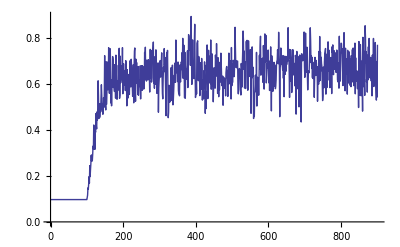

```mathematica
ListLinePlot[Flatten[t9]]
```

```mathematica
t9high=Drop[Flatten[t9],200];
```

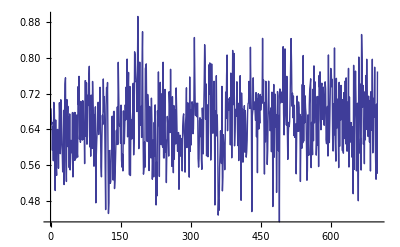

```mathematica
ListLinePlot[t9high]
```

```mathematica
Mean[t9high]
```

0.657212

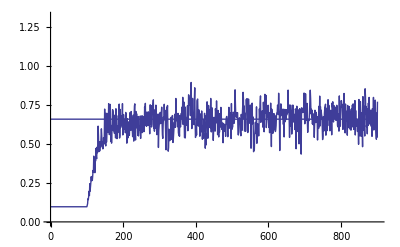

```mathematica
Show[Plot[0.657212,{x,0,900}],ListLinePlot[Flatten[t9]]]
```

```mathematica
ListLinePlot[t91]
```

-Graphics-

```mathematica
ListLinePlot[t81]
```

-Graphics-